```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"velocity tools","init.nb"}]];
```

## Building Definitions

## Output Forms / Generated Planes

### Definitions

```mathematica
(* Is c between a and b? *)
Between2D[a_,c_,b_]:=Norm[c]*a.b<Norm[b]*a.c&&Norm[c]*a.b<Norm[a]*b.c
Between3D[a_,c_,b_]:=Cross[a,b]*Cross[a,c]>=0&&Cross[c,b]*Cross[c,a]>=0
```

```mathematica
Clear[p,p2]
p[u_,v_,c_:{0,0},t0_:0]:=Function[{x,y},Evaluate[
z/.First@Solve[
Cross[Append[u,1+t0],Append[v,1+t0]].({x,y,z}-Append[c,0])==0,
{z}]
]]
p2[u_,v_,c_:{0,0},t0_:0]:=Function[{x,y},Evaluate[
If[Evaluate[Between2D[u,{x,y},v]],
Evaluate[p[u,v,c,t0][x,y]],
-Infinity
]
]]
p3[u_,v_,c_:{0,0},t0_:0]:=Function[{x,y},Evaluate[
If[Evaluate[Between2D[u,{x,y},v]],
Evaluate[p[u,v,c,t0][x,y]],
Infinity
]
]]

max2[fs___Function]:=Function[{u,v},Evaluate[
Max[#[u,v]&/@{fs}]
]]
min2[fs___Function]:=Function[{u,v},Evaluate[
Min[#[u,v]&/@{fs}]
]]
```

### Examples

Function[{u$,v$},Max[If[0<√2 (-u$+v$)&&0<√2 (u$+v$),v$,-∞],If[7/4 √(Abs[u$]^2+Abs[v$]^2)<1/4 √37 (u$+v$)&&7/4 √(Abs[u$]^2+Abs[v$]^2)<√2 ((3 u$)/2+v$/4),1/5 (3 u$+2 v$),-∞]]]

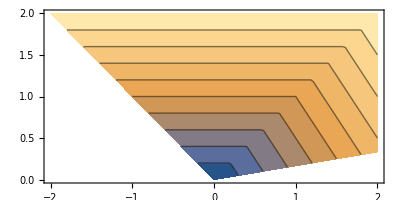

```mathematica
Γ=max2[p2[{-1,1},{1,1}],p2[{1,1},{3/2,1/4}]]
ContourPlot[Γ[u,v],{u,-2,2},{v,0,2},AspectRatio->{1,1}]
```

```mathematica
sliceVerts={{-1,1},{1,1},{3/2,1/4}};
Γ=max2@@(p2@@@Most@rotatedPairs[sliceVerts])
ContourPlot[Γ[u,v],{u,-2,2},{v,0,2},AspectRatio->{1,1}]
```

Function[{u$,v$},Max[If[0<√2 (-u$+v$)&&0<√2 (u$+v$),v$,-∞],If[7/4 √(Abs[u$]^2+Abs[v$]^2)<1/4 √37 (u$+v$)&&7/4 √(Abs[u$]^2+Abs[v$]^2)<√2 ((3 u$)/2+v$/4),1/5 (3 u$+2 v$),-∞]]]

Infinity::indet: Indeterminate expression -∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

Function[{u$,v$},Max[If[0<√2 (-u$+v$)&&0<√2 (u$+v$),v$,-∞],If[-0.25 √(Abs[u$]^2+Abs[v$]^2)<0.25 (-u$+v$)&&-0.25 √(Abs[u$]^2+Abs[v$]^2)<0.353553 u$,-4. (-u$-1.25 v$),-∞],If[0.25 √(Abs[u$]^2+Abs[v$]^2)<0.25 (u$+v$)&&0.25 √(Abs[u$]^2+Abs[v$]^2)<0.353553 u$,-4. (-u$+0.75 v$),-∞],If[0.375 √(Abs[u$]^2+Abs[v$]^2)<0.25 ((3 u$)/2+v$/4)&&0.375 √(Abs[u$]^2+Abs[v$]^2)<0.380173 u$,-16. (-0.25 u$+1.25 v$),-∞],If[7/4 √(Abs[u$]^2+Abs[v$]^2)<1/4 √37 (u$+v$)&&7/4 √(Abs[u$]^2+Abs[v$]^2)<√2 ((3 u$)/2+v$/4),1/5 (3 u$+2 v$),-∞]]]

Infinity::indet: Indeterminate expression -∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

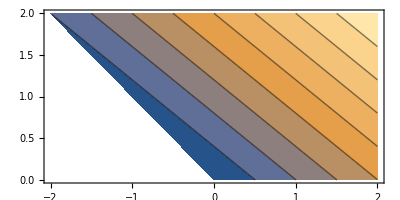

```mathematica
(* this is wrong bc its slower than above but slip should kick in ... this works for fast s1 *)
s1=.25;
sliceVerts={{-1,1},{1,1},{3/2,1/4}};
Γ=max2[
Sequence@@Join[
p2[#,{s1,0}]&/@sliceVerts,
p2@@@Most@rotatedPairs[sliceVerts]]
]
ContourPlot[Γ[u,v],{u,-2,2},{v,0,2},AspectRatio->{1,1}]
```

Function[{u$,v$},Max[If[0<√2 (-u$+v$)&&0<√2 (u$+v$),v$,-∞],If[7/4 √(Abs[u$]^2+Abs[v$]^2)<1/4 √37 (u$+v$)&&7/4 √(Abs[u$]^2+Abs[v$]^2)<√2 ((3 u$)/2+v$/4),1/5 (3 u$+2 v$),-∞],Min[If[-0.25 √(Abs[u$]^2+Abs[v$]^2)<0.25 (-u$+v$)&&-0.25 √(Abs[u$]^2+Abs[v$]^2)<0.353553 u$,-4. (-u$-1.25 v$),-∞],If[0.25 √(Abs[u$]^2+Abs[v$]^2)<0.25 (u$+v$)&&0.25 √(Abs[u$]^2+Abs[v$]^2)<0.353553 u$,-4. (-u$+0.75 v$),-∞],If[0.375 √(Abs[u$]^2+Abs[v$]^2)<0.25 ((3 u$)/2+v$/4)&&0.375 √(Abs[u$]^2+Abs[v$]^2)<0.380173 u$,-16. (-0.25 u$+1.25 v$),-∞]]]]

Infinity::indet: Indeterminate expression -∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

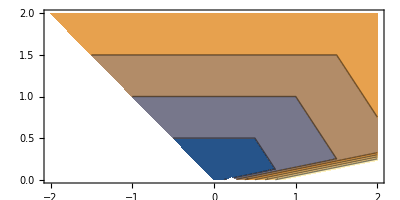

```mathematica
(* I think this and the next one are correct, doesn't work for fast s1 *)
s1=.25;
sliceVerts={{-1,1},{1,1},{3/2,1/4}};
Γ=max2[
Sequence@@{
min2@@(p2[#,{s1,0}]&/@sliceVerts),
max2@@(p2@@@Most@rotatedPairs[sliceVerts])
}
]
ContourPlot[Γ[u,v],{u,-2,2},{v,0,2},AspectRatio->{1,1}]
```

First::nofirst: {} has zero length and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Function[{u$,v$},Max[If[0<√2 (-u$+v$)&&0<√2 (u$+v$),v$,-∞],If[7/4 √(Abs[u$]^2+Abs[v$]^2)<1/4 √37 (u$+v$)&&7/4 √(Abs[u$]^2+Abs[v$]^2)<√2 ((3 u$)/2+v$/4),1/5 (3 u$+2 v$),-∞],If[9/4 √(Abs[u$]^2+Abs[v$]^2)<3/2 ((3 u$)/2+v$/4)&&9/4 √(Abs[u$]^2+Abs[v$]^2)<(3 √37 u$)/8,(2 u$)/3,-∞],Min[If[-0.25 √(Abs[u$]^2+Abs[v$]^2)<0.25 (-u$+v$)&&-0.25 √(Abs[u$]^2+Abs[v$]^2)<0.353553 u$,-4. (-u$-1.25 v$),-∞],If[0.25 √(Abs[u$]^2+Abs[v$]^2)<0.25 (u$+v$)&&0.25 √(Abs[u$]^2+Abs[v$]^2)<0.353553 u$,-4. (-u$+0.75 v$),-∞],If[0.375 √(Abs[u$]^2+Abs[v$]^2)<0.375 u$&&0.375 √(Abs[u$]^2+Abs[v$]^2)<0.375 u$,z/.First[{}],-∞],If[0.375 √(Abs[u$]^2+Abs[v$]^2)<0.25 ((3 u$)/2+v$/4)&&0.375 √(Abs[u$]^2+Abs[v$]^2)<0.380173 u$,-16. (-0.25 u$+1.25 v$),-∞]]]]

Infinity::indet: Indeterminate expression -∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

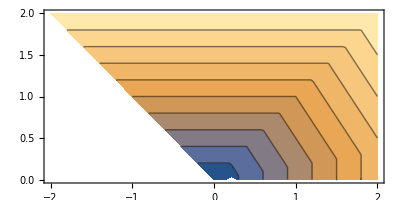

```mathematica
s1=.25;
sliceVerts={{-1,1},{1,1},{3/2,1/4},{3/2,0}};
Γ=max2[
Sequence@@{
min2@@(p2[#,{s1,0}]&/@sliceVerts),
max2@@(p2@@@Most@rotatedPairs[sliceVerts])
}
]
ContourPlot[Γ[u,v],{u,-2,2},{v,0,2},AspectRatio->{1,1}]
```

First::nofirst: {} has zero length and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Function[{u$,v$},Min[If[-1.6 √(Abs[u$]^2+Abs[v$]^2)<1.6 (-u$+v$)&&-1.6 √(Abs[u$]^2+Abs[v$]^2)<2.26274 u$,-0.625 (-u$-2.6 v$),∞],If[1.6 √(Abs[u$]^2+Abs[v$]^2)<1.6 (u$+v$)&&1.6 √(Abs[u$]^2+Abs[v$]^2)<2.26274 u$,-0.625 (-u$-0.6 v$),∞],If[2.4 √(Abs[u$]^2+Abs[v$]^2)<2.4 u$&&2.4 √(Abs[u$]^2+Abs[v$]^2)<2.4 u$,z/.First[{}],∞],If[2.4 √(Abs[u$]^2+Abs[v$]^2)<1.6 ((3 u$)/2+v$/4)&&2.4 √(Abs[u$]^2+Abs[v$]^2)<2.43311 u$,-2.5 (-0.25 u$-0.1 v$),∞],Max[If[0<√2 (-u$+v$)&&0<√2 (u$+v$),v$,-∞],If[7/4 √(Abs[u$]^2+Abs[v$]^2)<1/4 √37 (u$+v$)&&7/4 √(Abs[u$]^2+Abs[v$]^2)<√2 ((3 u$)/2+v$/4),1/5 (3 u$+2 v$),-∞],If[9/4 √(Abs[u$]^2+Abs[v$]^2)<3/2 ((3 u$)/2+v$/4)&&9/4 √(Abs[u$]^2+Abs[v$]^2)<(3 √37 u$)/8,(2 u$)/3,-∞]]]]

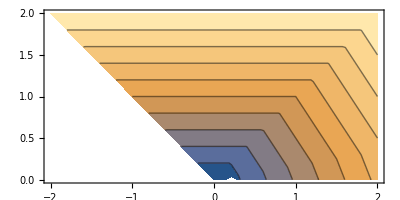

```mathematica
(* this could be it *)
s1=1.6;
sliceVerts={{-1,1},{1,1},{3/2,1/4},{3/2,0}};
Γ=min2[
Sequence@@{
min2@@(p3[#,{s1,0}]&/@sliceVerts),(* gives no sol for vert of form {v,0} *)
max2@@(p2@@@Most@rotatedPairs[sliceVerts])
}
]
ContourPlot[Γ[u,v],{u,-2,2},{v,0,2},AspectRatio->{1,1}]
```

```mathematica
ListAnimate[Table[
sliceVerts={{-1,1},{1,1},{3/2,1/4},{3/2,0}};
Γ=Quiet@min2[
Sequence@@{
min2@@(p3[#,{s1,0}]&/@sliceVerts),
max2@@(p2@@@Most@rotatedPairs[sliceVerts])
}
];
Quiet@ContourPlot[Γ[u,v],{u,-2,2},{v,0,2},AspectRatio->{1,1},PlotLabel->s1],
{s1,1,2,.1}]]
```

## Examples

## Ex 1. Simple 2 Region Problem

### Setup

```mathematica
defVel[F0,{{1,-1},{1,1},{-1,1},{-1,-1}}]
defVel[F1,#+{0.5,0}&/@{{1,-1},{1,1},{-1,1},{-1,-1}}]
{LabeledPolarHullPlot[F0],LabeledPolarHullPlot[F1]}
```

{-Graphics-,-Graphics-}

```mathematica
M0=ImplicitRegion[y<=0,{x,y}];
M1=ImplicitRegion[y>=0,{x,y}];
Σ=RegionIntersection[M0,M1]
Simplify[{x,y},{x,y}∈Σ]
```

ImplicitRegion[y==0,{x,y}]

{x,0}

```mathematica
x0=-{0,1};

Subscript[Γ, 0]=Function[{x,y},Evaluate@If[RegionMember[M0,{x,y}],
Evaluate@Max[#1.({x,y}-x0)/#1.#2&@@@({rotationNormals[Subscript[F0, pt]],Subscript[F0, pt]}ᵀ)],
-Infinity
]]
```

Function[{x,y},If[(x|y)∈ℝ&&y≤0,Max[-x,x,-1-y,1+y],-∞]]

### Γ_Σ & pwlSubgrads

```mathematica
Subscript[Γ, Σ]=Function[{x},Evaluate@Simplify[Subscript[Γ, 0][x,y],{x,y}∈Σ]]
```

Function[{x},Max[1,-x,x]]

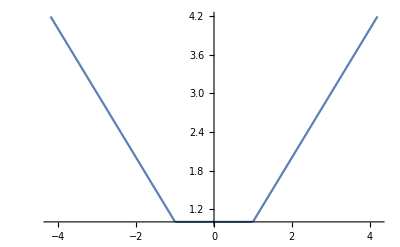

```mathematica
Plot[Subscript[Γ, Σ][x],{x,-4.2,4.2}]
```

```mathematica
{#,#//InputForm}&@D[Subscript[Γ, Σ][x], x]
```

{Piecewise[{{-1, x<-1}, {0, -1<x<1}, {1, x>1}, {Indeterminate, True}}],Piecewise[{{-1, x < -1}, {0, Inequality[-1, Less, x, Less, 1]}, {1, x > 1}}, Indeterminate]}

```mathematica
subgrad[f_,x_]:=pwlSubgrads[D[f, x]]
Clear[pwlSubgrads]
pwlSubgrads[Piecewise[pairs_List,Indeterminate]]:=Module[{},
coneSubgrads={#1[[1]]<ζ<#2[[1]],Reduce[And[#1[[2]],#2[[2]]]/.{Less->LessEqual,Greater->GreaterEqual}]}&@@@Most@rotatedPairs@pairs;
Piecewise[Riffle[pairs,coneSubgrads]]
]

pwlSubgrads[D[Subscript[Γ, Σ][x], x]]
```

Piecewise::pairs: The first argument pairs_List of Piecewise is not a list of pairs.

Piecewise[{{-1, x<-1}, {-1<ζ<0, x==-1}, {0, -1<x<1}, {0<ζ<1, x==1}, {1, x>1}, {0, True}}]

```mathematica
xσ={-1,0}
t=Subscript[γ, F0][xσ-x0]
v0=(xσ-x0)/t
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* points in normal cone properly scaled *)
ζ1s=Subscript[RefractedNormals, F1][ζ0]
v2s=(𝒩̂)_(F1^°)/@ζ1s
(* rounding errors in ζvLink[F1][θ] lead to 0's <- needs to be fixed with dictionary approach *)
v2s=(If[Head@#===List,#,Null]&/@v2s)/.Null->Sequence[]
(* using simple cone handling *)
v2s=If[ConeQ[#] ,{#/.{λ->0},#/.{λ->1}},#]&/@v2s
(*v2s=Select[v2s,NonNegative@Last@#&]*)
```

{-1,0}

1

{-1,1}

{-1+λ,λ}

{{0.,-1.},{0.,1.},{0.+0.666667 (1-λ),0.-1. λ},{0.+0.666667 (1-λ),0.+1. λ},{0.-2. λ,0.+1. (1-λ)},{0.-2. λ,0.-1. (1-λ)}}

{{1.5 (1-λ)-0.5 λ,-1},{-0.5 (1-λ)+1.5 λ,1},{1.5,-1},{1.5,1},{-0.5,1},0}

{{1.5 (1-λ)-0.5 λ,-1},{-0.5 (1-λ)+1.5 λ,1},{1.5,-1},{1.5,1},{-0.5,1}}

{{{1.5,-1},{-0.5,-1}},{{-0.5,1},{1.5,1}},{1.5,-1},{1.5,1},{-0.5,1}}

```mathematica
ζvLink[F1][θ]
```

Piecewise[{{{1.5,-1}, -π/2<θ<0.}, {{1.5,1}, 0.<θ<π/2}, {{-0.5,1}, π/2<θ<3.14159}, {{-0.5,-1}, 3.14159<θ<(3 π)/2}, {{1.5 (1-λ)-0.5 λ,-1}, θ==-π/2}, {{1.5 (1-λ)+1.5 λ,1-2 λ}, θ==0.}, {{-0.5 (1-λ)+1.5 λ,1}, θ==π/2}, {{-0.5 (1-λ)-0.5 λ,-1+2 λ}, θ==3.14159}, {0, True}}]

```mathematica
t00=Subscript[γ, F0][y0-x0]
v0=(y0-x0)/t00
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* normal cone points *)
ζ2s=Subscript[RefractedNormals, F1][ζ0]
(𝒩̂)_(F1^°)/@ζ2s
v2s=Select[discretize/@(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&]
```

```mathematica
Subscript[RefractedVelocities, F1][ζ00,n]
```

{}